```mathematica
Nt = 10;
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;
Nx = 10; 
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax)
method = "CN";
```

1

```mathematica
T = Table[tn = ti + n *deltat, {n, 0, Nt }];


(*For Perodic Interpolation*) 
X = Table[xm = xi + m *deltax, {m, 0, Nx + 1}];
(*For Everything Else*)
X2 =  Table[xm = xi + m *deltax, {m, 0, Nx }];
```

```mathematica
U = Table[0, {n, 0, Nt}, {m, 0, Nx}];
```

```mathematica
f[x_] = Exp[-16* x^2];
U[[1,All]] = f[X2]//N;
```

```mathematica
U = Chop[N[U], 10^(-307)];
U = N[U];
U = Developer`ToPackedArray[U, Real]; 
Developer`PackedArrayQ[U]
```

True

```mathematica
L = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
L = -1 * c * L ;
L//MatrixForm;

I1 = IdentityMatrix[Length[L]];
```

```mathematica
(* Trapezoidal *)
Ut = Table[0, {n, 0, Nt }, {m, 0, Nx }];
Ut[[1,All]] = f[X2]//N;
Ut = Chop[N[Ut], 10^(-307)];
Ut = N[Ut];
Ut = Developer`ToPackedArray[Ut, Real]; 
Developer`PackedArrayQ[Ut]
```

True

```mathematica
A = I1 - ((deltat / 2) * L);
B = I1 + ((deltat / 2) * L);
M = Inverse[A].B;
Do[Ut[[n+1,All]] = M.Ut[[n,All]], {n,1,Nt}];

(* Euler *)
Ue = Table[0, {n, 0, Nt }, {m, 0, Nx }];
Ue[[1,All]] = f[X2]//N;
Ue = Chop[N[Ue], 10^(-307)];
Ue = N[Ue];
Ue = Developer`ToPackedArray[Ue, Real]; 
Developer`PackedArrayQ[Ue] 

Leuler = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
Leuler = -1 * c * Leuler ;
Leuler//MatrixForm;

Ieuler = IdentityMatrix[Length[Leuler]];

euler = Ieuler + deltat*Leuler;
Do[Ue[[n+1,All]] = euler.Ue[[n,All]], {n,1,Nt}];
```

True

```mathematica
(*RK2*)
Urk = Table[0, {n, 0, Nt }, {m, 0, Nx }];
Urk[[1,All]] = f[X2]//N;
Urk = Chop[N[Urk], 10^(-307)];
Urk = N[Urk];
Urk = Developer`ToPackedArray[Urk, Real]; 
Developer`PackedArrayQ[Urk]

LRK2 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LRK2 = -1 * c * LRK2 ;
LRK2//MatrixForm;

LRK22 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->2, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
LRK22//MatrixForm;

IRK2 = IdentityMatrix[Length[LRK2]];

Mrk = (IRK2 + (deltat * LRK2) + ((1/2)* (deltat^2) * (-c)^2 * LRK22));

Do[Urk[[n+1,All]] = Mrk.Urk[[n,All]], {n,1,Nt}];
```

True

```mathematica
(************************************************************************************************************************)

(* Eigenvalues*)
```

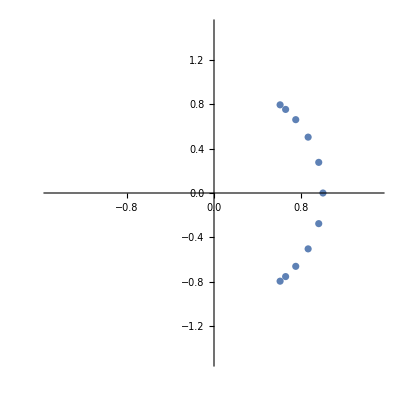

```mathematica
(*Trapezoidal*)
evals = Eigenvalues[N[M]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

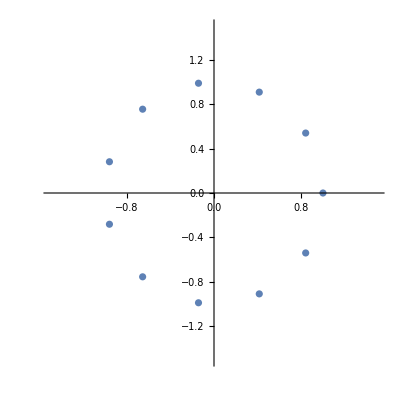

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[euler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
Abs[evalsEuler]
ListPlot[{Transpose[{realEvalsEuler,imagEvalsEuler}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[Mrk]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
Abs[evalsRK2]
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]

(************************************************************************************************************************)
(*Export*)
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

-Graphics-

```mathematica
(*exportData=Flatten/@Transpose[{realEvals,imagEvals}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_"<>method<>"_"<>ToString[r]<>".dat",exportData,"Table"];*)
```

```mathematica
Animate[ListPlot[Table[Ut[[n+1, m+1]], {m,0,Nx }], PlotRange->{All,{0,2}}], {n,0,Nt,1}]
Animate[ListPlot[Table[Urk[[n+1, m+1]], {m,0,Nx }], PlotRange->{All,{0,2}}], {n,0,Nt,1}]
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
PadeApproximant[Exp[x],{x,0,{2,2}}]
```

(1+x/2+x^2/12)/(1-x/2+x^2/12)

```mathematica
PadeApproximant[Exp[x],{x,0,{4,4}}]
```

(1+x/2+(3 x^2)/28+x^3/84+x^4/1680)/(1-x/2+(3 x^2)/28-x^3/84+x^4/1680)

```mathematica
Series[Exp[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5